Average Run Length (ARL)

A Run is a sequence of adjacent numbers that are within the LCL and UCL.
(Illustrate this using the document camera)

The Average Run Length is the average time between sample means that fall out of bounds,
or outside the [LCL,UCL] interval.

Use simulation to estimate the ARL. Let

	Z~Normal[0,1]

Then μ=0 and σ=1 and the control limits are

	upper control limit=UCL=μ+3σ=3
lower control limit=LCL=μ-3σ=-3

How would you estimate the average run length? (Discuss)








(1) Draw a random sample of size n_ from the population Z~Normal[0,1]
and plot the values.
(2) Identify the points that are out of bounds (outside the LCL, UCL lines).
(3) Count the number of samples between these points, these are the runs.
(4) Compute the average length of all the runs.

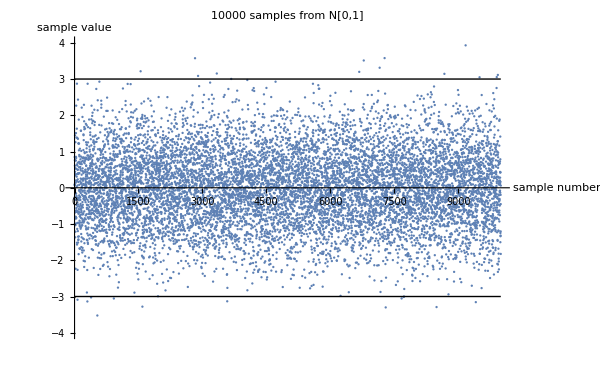

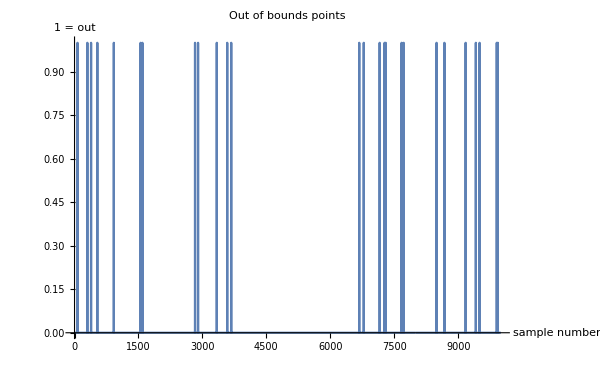

n = 10000

Number out of control = 26

Probability of being out of control (p) = 0.0026

ARL = 1/p = 394.44

```mathematica
n=10^4;
list=RandomVariate[NormalDistribution[0,1],n];
Show[
ListPlot[list,PlotRange->{{-0.5,n+0.5},{-4.0,4.0}},
PlotLabel->Row[{Style[ToString[n],14,Blue],Style[" samples from N[0,1]",15,Blue]}],
AxesLabel->{Style["sample number",14,Blue],Style["sample value",14,Blue]},
ImageSize->{600,500}],
Graphics[{
Line[{{0,3},{n,3}}],
Line[{{0,-3},{n,-3}}]
}]
]
out=Table[If[-3<list[[i]]<3,0,1],{i,1,n}];
ListLinePlot[out,PlotLabel->Style["Out of bounds points",15,Blue],
AxesLabel->{Style["sample number",14,Blue],Style["1 = out",14,Blue]},
ImageSize->{600,500}]
pos=Flatten[Position[out,1]];
rl=Differences[pos];
arl=N[Mean[rl]];

Print[Style["n = ",18,Blue],Style[n,18,Blue]]
Print[Style["Number out of control = ",18,Blue],Style[Length[Flatten[pos]],18,Blue]]
Print[Style["Probability of being out of control (p) = ",18,Blue],Style[N[Length[Flatten[pos]]/n],18,Blue]]
Print[Style["ARL = 1/p = ",18,Blue],Style[arl,18,Blue]]
```

Average Run Length (ARL) is different every time. Why? (sample)

What is the population ARL?


1) Calculate the probability of being out of control when the process is described by
	Z~Normal[0,1]

	p=P(out of control)
=P(Z>UCL OR Z<LCL)
=P(Z>3 OR Z<-3)
=P(Z>3)+P(Z<-3)-P(Z>3 AND Z<-3)
=(1-P(Z≤3))+P(Z<-3)
=2P(Z<-3)
=2CDF[NormalDistribution[0,1],-3]

2) Then ARL=1/p. (Why?)

(discuss using document cam)

```mathematica
p=2CDF[NormalDistribution[0.0,1.0/3],-1.0];
arl=1/p;
Print[Style["Probability of being out of control (p) = ",18,Blue],Style[p,18,Blue]]
Print[Style["ARL = 1/p = ",18,Blue],Style[arl,18,Blue]]
```

Probability of being out of control (p) = 0.0026998

ARL = 1/p = 370.398

Now, assume the process changes (new process) so that μ changes from 0 to 0.5
but, no ones knows it changed. Consequently, the LCL and UCL do not change!!!

What is the new ARL, meaning what is the average number of samples before you see a sample
out of control for the new process?

The new process is described by

	X~Normal[0.5,1]

Remember: LCL=μ-3σ. UCL=μ+3σ

1) Calculate the probability of being out of control.

	p=P(out of control)
=P(X>UCL ∪ X<LCL)
=P(X>3 ∪ X<-3)
=P(X>3)+P(X<-3)-P(X>3 ∩ X<-3)
=(1-P(X≤3))+P(X<-3)
=(1-CDF[NormalDistribution[0.5,1],3])+CDF[NormalDistribution[0.5,1],-3]

2) Then ARL=1/p.

```mathematica
p=(1.0-CDF[NormalDistribution[0.5,1.0],3.0])+CDF[NormalDistribution[0.5,1.0],-3.0];
arl=1/p;
Print[Style["Probability of being out of control (p) = ",18,Blue],Style[p,18,Blue]]
Print[Style["ARL = 1/p = ",18,Blue],Style[arl,18,Blue]]
```

Probability of being out of control (p) = 0.00644229

ARL = 1/p = 155.224

What does the shift in mean need to be before the ARL would be 30?

The new process is described by

	Y~Normal[μ,1]

but μ is unknown.

Since we want an ARL of 30, then p=1/ARL=1/30=0.03333.

1) Calculate the probability of being out of control. Very important!

	(a) 0.03333=p=P(out of control)
=P(Y>UCL ∪ Y<LCL)
=P(Y>μ+3σ ∩ Y<μ-3σ)
=(1-P(Y<μ+3))+P(Y<μ-3) 
		(remember, σ=1)
		
			OR
	
	(b) 0.03333=p=P(out of control)
=P(Y>UCL ∪ Y<LCL)
=P(Y>3σ ∪ Y<-3σ)
=(1-P(Y<3))+P(Y<3) 
		(remember, σ=1)

Discuss, why?
	
	
	
	
	
	
	
	
newmean=FindRoot[(1-CDF[Normalistribution[m,1],3])+
CDF[Normalistribution[m,1],-3]==0.03333,{m,1}]

```mathematica
nm=FindRoot[1.0-CDF[NormalDistribution[m,1.0],3.0]+
CDF[NormalDistribution[m,1.0],-3.0]==0.03333,{m,1}];

Print[Style["new mean = ",18,Blue],Style[nm,18,Blue]]
```

new mean = {m→1.16583}

Let’s check it. The new process is described by

	Y~Normal[1.16583,1]

1) Calculate the probability of being out of control.

	p=P(out of control)
=P(Y>UCL ∪ Y<LCL)
=P(Y>3 ∪ Y<-3)
=P(Y>3)+P(Y<-3)-P(Y>3 ∩ Y<-3)
=(1-P(Y<3))+P(Y<-3)
=(1-CDF[NormalDistribution[1.16583,1],3])+
CDF[NormalDistribution[1.16583,1],-3]

2) Then ARL=1/p

```mathematica
p=1.0-CDF[NormalDistribution[1.16583,1.0],3.0]+CDF[NormalDistribution[1.16583,1.0],-3.0];
arl=1/p;
Print[Style["Probability of being out of control (p) = ",18,Blue],Style[p,18,Blue]]
Print[Style["ARL = 1/p = ",18,Blue],Style[arl,18,Blue]]
```

Probability of being out of control (p) = 0.0333299

ARL = 1/p = 30.0031